# Variants US analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/variants-us-summary

```mathematica
dataset="variants-us-summary";
```

## Setup

### Variants

```mathematica
variants={"other","Alpha","Gamma","Delta","Iota","BA.1","BA.2","BA.4","BA.5","BA.2.12.1","BQ.1"};
```

```mathematica
variantLabels={"other","Alpha","Gamma","Delta","Iota","BA.1","BA.2","BA.4","BA.5","BA.2.12.1","BQ.1"};
```

```mathematica
n=Length[variants]
```

11

### Colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.07;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
colors=Join[{Gray},makeColors[n-1]]
```

{GrayLevel[0.5],RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.24570506666666667, 0.32803275555555556, 0.8046117333333334],RGBColor[0.2816870488888889, 0.5253491911111111, 0.7779425822222222],RGBColor[0.36232965333333333, 0.6569880666666666, 0.6428821066666668],RGBColor[0.4851872222222222, 0.72043824, 0.47433784000000007],RGBColor[0.6366506844444445, 0.7433824044444445, 0.34089374666666666],RGBColor[0.7885816, 0.7225868666666666, 0.26338486666666666],RGBColor[0.884846471111111, 0.6207400666666666, 0.22517370666666667],RGBColor[0.8977938177777778, 0.4210983288888889, 0.18556725333333332],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
Map[rgbColorToHex,colors]
```

{#80,#4D21AD,#3F54CD,#4886C6,#5CA8A4,#7CB879,#A2BE57,#C9B843,#E29E39,#E56B2F,#DB2823}

```mathematica
legendPanel=PointLegend[colors[[2;;n]],variantLabels[[2;;n]],LegendMarkerSize->20,LegendLayout->{"Column",1},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}]
```

{other→GrayLevel[0.5],Alpha→RGBColor[0.30382016, 0.13051672, 0.67703096],Gamma→RGBColor[0.24570506666666667, 0.32803275555555556, 0.8046117333333334],Delta→RGBColor[0.2816870488888889, 0.5253491911111111, 0.7779425822222222],Iota→RGBColor[0.36232965333333333, 0.6569880666666666, 0.6428821066666668],BA.1→RGBColor[0.4851872222222222, 0.72043824, 0.47433784000000007],BA.2→RGBColor[0.6366506844444445, 0.7433824044444445, 0.34089374666666666],BA.4→RGBColor[0.7885816, 0.7225868666666666, 0.26338486666666666],BA.5→RGBColor[0.884846471111111, 0.6207400666666666, 0.22517370666666667],BA.2.12.1→RGBColor[0.8977938177777778, 0.4210983288888889, 0.18556725333333332],BQ.1→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}]
```

{other→1,Alpha→2,Gamma→3,Delta→4,Iota→5,BA.1→6,BA.2→7,BA.4→8,BA.5→9,BA.2.12.1→10,BQ.1→11}

### Date ticks

```mathematica
dateTicks={"2021-01-01","2021-03-01","2021-05-01","2021-07-01","2021-09-01","2021-11-01","2022-01-01","2022-03-01","2022-05-01","2022-07-01","2022-09-01","2022-11-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-01-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-11-15

```mathematica
countries=Union[seqData[[All,2]]]
```

{USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{USA→{{2022-11-01,2050},{2022-11-02,1566},{2022-11-03,1832},{2022-11-04,1599},{2022-11-05,1109},{2022-11-06,1289},{2022-11-07,2117},{2022-11-08,1429},{2022-11-09,1035},{2022-11-10,731},{2022-11-11,513},{2022-11-12,458},{2022-11-13,306},{2022-11-14,303},{2022-11-15,31}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

```mathematica
variantSeries=Map[smoothedPrevalence[countryVariantCounts["USA",#],countrySequenceCounts["USA"]]&,variants];
```

```mathematica
accumulateDateSeries[series_]:=Module[{n,dates,prependedSeries,accumulatedValues},
n=Length[series];
dates=series[[1,All,1]];
prependedSeries=Prepend[series,Map[{#,0}&,dates]];
accumulatedValues=Accumulate[prependedSeries[[All,All,2]]];
Table[Transpose[{dates,accumulatedValues[[i]]}],{i,n+1}]
]
```

```mathematica
accumulatedSeries=accumulateDateSeries[variantSeries];
```

```mathematica
annotationData={{"Alpha","2021-03-10",0.77},{"Delta","2021-06-15",0.90},{"BA.1","2021-12-25",0.93},{"BA.2.12.1","2022-04-04",0.97},{"BA.5","2022-08-01",0.91}};
```

```mathematica
annotations=Map[{Text[Style[#[[1]],White,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],{#[[2]],#[[3]]},{-1,1}]}&,annotationData];
```

```mathematica
freqPlotAccumulated[variantSeries_]:=DateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Variant frequency"},PlotTheme->"FullAxes",ImageSize->400,AspectRatio->0.55,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,1}},DateTicksFormat->{"MonthNameShort"},PlotStyle->Map[Directive[#,Thickness[0.003]]&,Reverse[colors]],Filling->Table[i->{Axis,Lighter[Reverse[colors][[i]],0.6]},{i,1,n}],FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,0.2]],Automatic},{dateTicks,Automatic}},Epilog->annotations]
```

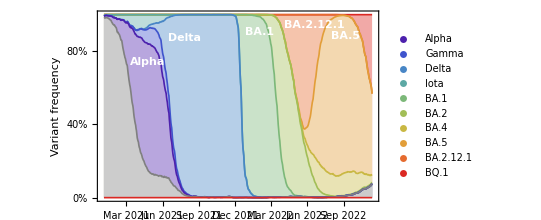

```mathematica
figFreq=Legended[freqPlotAccumulated[accumulatedSeries],Placed[legendPanel,Right]]
```

```mathematica
Export["figures/"<>dataset<>"_freq-stacked.png",figFreq,"PNG",ImageResolution->300]
```

figures/variants-us-summary_freq-stacked.png

## Partitioned cases

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

```mathematica
variantSeries=Map[csVariantGather["USA",#]&,variants];
```

```mathematica
accumulateDateSeries[series_]:=Module[{n,dates,prependedSeries,accumulatedValues},
n=Length[series];
dates=series[[1,All,1]];
prependedSeries=Prepend[series,Map[{#,0}&,dates]];
accumulatedValues=Accumulate[prependedSeries[[All,All,2]]];
Table[Transpose[{dates,accumulatedValues[[i]]}],{i,n+1}]
]
```

```mathematica
accumulatedSeries=accumulateDateSeries[variantSeries];
```

```mathematica
annotationData={{"Delta","2021-08-10",90000},{"BA.1","2021-12-20",140000},{"BA.5","2022-07-10",80000}};
```

```mathematica
annotations=Map[{Text[Style[#[[1]],White,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],{#[[2]],#[[3]]},{-1,1}]}&,annotationData];
```

```mathematica
splitCasePlotAccumulated[variantSeries_]:=DateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Variant cases"},PlotTheme->"FullAxes",ImageSize->400,AspectRatio->0.55,ImagePadding->{{58,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"},PlotStyle->Map[Directive[#,Thickness[0.003]]&,Reverse[colors]],Filling->Table[i->{i+1,Lighter[Reverse[colors][[i]],0.6]},{i,n}],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Epilog->annotations]
```

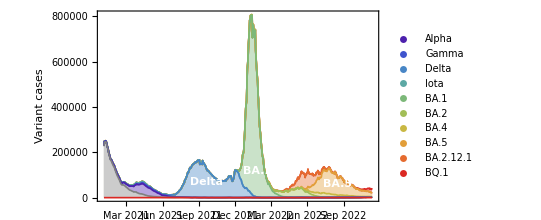

```mathematica
figCases=Legended[splitCasePlotAccumulated[accumulatedSeries],Placed[legendPanel,Right]]
```

```mathematica
Export["figures/"<>dataset<>"_cases-stacked.png",figCases,"PNG",ImageResolution->300]
```

figures/variants-us-summary_cases-stacked.png